```mathematica
(* 1.1.3.6 *)
-Graphics-
(* Условие *)
-Graphics-
-Graphics-

(* 1. Функция Гамильтона. *)
(* Из условий задачи можно понять, что мы рассматриваем наш электрон в рамках модели классической частицы, то есть на него не действуют эффекты квантовой механики, значит функция , а как следствие и уравнения Гамильтона описывают динамику движения нашей частицы в металле.  Но  особенность заключается в том, что выражение кинетической энергии и импульса не описываются квадратом величины(поскольку нет гладкой параболической зависимости), а есть лишь негладкое модульное выражение, что является характерной особенностью для данной конкретной системы и ее закона дисперсии. Запишем выражения для функции Гамильтона под действием потенциала нано-неоднородности, т.е. потенциала, вызванный наноразмерным дефектом в металле. *)
```

```mathematica
ℋ =Subscript[v, ℱ] Abs[p[t]] +a  Abs[x[t]]
```

a Abs[x[t]]+Abs[p[t]] v_ℱ

```mathematica
(* Где : "v_ℱ ≈ 2×10^8[cm]/[sec]" - скорость Ферми - такая скорость электрона, которая достигается при движении на уровне энергии Ферми, "ℰ = v_ℱ|p[t]|" - энергия электрона с импульсом "p" в металле, "𝒰(x) = a|x[t]|" - треугольный потенциал  нано - неоднородсти, где "a = 1.6×10^-5([g][cm])/[sec]^2" *)
```

```mathematica
(* Запишем уравнения Гамильтона для нашей системы, которые могут быть разбиты на 4 пары (из-за разных возможностей раскрытия модуля) *)
```

```mathematica
D[p[t], t] == - a (* Импульс и координата положительные *)
D[x[t], t] == Subscript[v, ℱ]

D[p[t], t] ==  a (* Импульс и координата отрицательные *)
D[x[t], t] == -Subscript[v, ℱ]

D[p[t], t] ==  a (* Импульс положительный, координата отрицательная *)
∂_t x[t] == Subscript[v, ℱ]

∂_t p[t] ==  -a (* Импульс отрицательный, координата положительная *)
D[x[t], t] == -Subscript[v, ℱ]

(* Четыре пары данных уравнений выражают линейные зависимости импульса и координаты, которые будут описывать на плоскости, подобия квадратов (что контрастирует с привычными для нас окружностями) *)
```

```mathematica
DSolve[{D[p[t], t] == - a,D[x[t], t] == Subscript[v, ℱ],p[0]==1,x[0]==1},{x[t],p[t]},t] (* Импульс и координата положительные *)
```

{{p[t]→1-a t,x[t]→1+t v_ℱ}}

```mathematica
DSolve[{D[p[t], t] ==  a,D[x[t], t] == -Subscript[v, ℱ],p[0]==-1,x[0]==-1},{x[t],p[t]},t](* Импульс и координата отрицательные *)
```

{{p[t]→-1+a t,x[t]→-1-t v_ℱ}}

```mathematica
DSolve[{D[p[t], t] ==  a,D[x[t], t] == Subscript[v, ℱ],p[0]==1,x[0]==-1},{x[t],p[t]},t](* Импульс положительный, координата отрицательная *)
```

{{p[t]→1+a t,x[t]→-1+t v_ℱ}}

```mathematica
DSolve[{D[p[t], t] ==  -a,D[x[t], t] ==- Subscript[v, ℱ],p[0]==-1,x[0]==1},{x[t],p[t]},t](* Импульс отрицательный, координата положительная *)
```

{{p[t]→-1-a t,x[t]→1-t v_ℱ}}

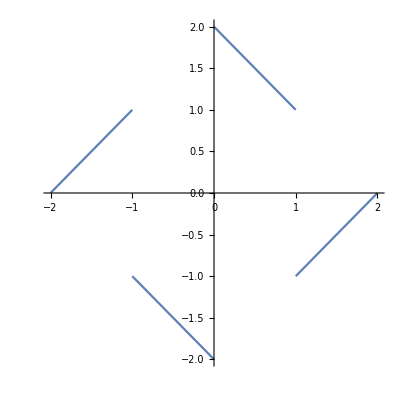

```mathematica
ParametricPlot[{{1-a t,1+t Subscript[v, ℱ]},{-1+a t,-1-t Subscript[v, ℱ]},{1+a t,-1+t Subscript[v, ℱ]},{-1-a t,1-t Subscript[v, ℱ]}}/.{ Subscript[v, ℱ]->1, a ->1},{t,0,1}, PlotPoints->100]
```

```mathematica
(* Изобразим функцию Гамильтона в фазовом пространстве и изучим различные уровни ее энергий (в упрощенном случае без учета значений констант). Помимо этого,также рассмотрим ее топографическую карту. *)
```

```mathematica
Plot3D[{Subscript[v, ℱ] Abs[p] +a  Abs[x],3}/.{ Subscript[v, ℱ]->1, a ->1}, {x,-5,5},{p,-5,5}, PlotRange->All]
```

-Graphics3D-

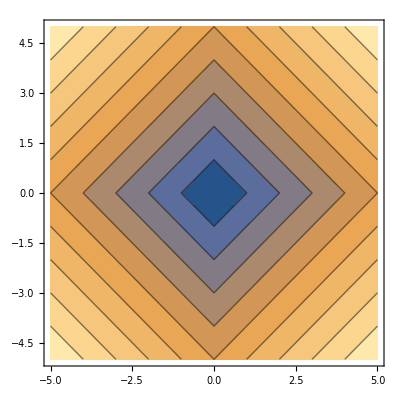

```mathematica
ContourPlot[Subscript[v, ℱ] Abs[p] +a  Abs[x]/.{ Subscript[v, ℱ]->1, a ->1}, {x,-5,5},{p,-5,5}]
```

```mathematica
(* Уровень нулевой энергии, то есть отсутствия всяческого движения и взаимодействия характеризуется нулевым импульсом и координатой и только. Что важно в данном случае, так это необычное описание уровней энергетических в фазовом пространстве, что мы и можем увидеть здесь из-за линейности изменения наших фазовых координат. Благодаря фазовому портрету  и топографической карте можно также узнать с каким периодом движется наш электрон в данном конкретном упрощенном случае - это будет величина площади конкретного энергетического уровня - т.е величина действия. А величина действия очевидно также будет расти линейно со временем из-за линейности роста энергии системы, изменения величин наших фазовых координат, а как следствие  и период движения электрона будет расти тоже линейнозависимо *)
```

```mathematica
(* Теперь же можно взглянуть на портреты случая не упрощенного  *)
```

```mathematica
Plot3D[{Subscript[v, ℱ] Abs[p] +a  Abs[x],200000000000000}/.{ Subscript[v, ℱ]->20000000, a ->0.00016}, {x,-50000000,50000000},{p,-50000000,50000000}, PlotRange->All]
```

-Graphics3D-

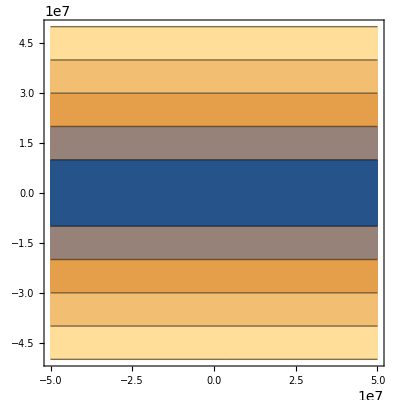

```mathematica
ContourPlot[{Subscript[v, ℱ] Abs[p] +a  Abs[x]}/.{ Subscript[v, ℱ]->20000000, a ->0.00016}, {x,-50000000,50000000},{p,-50000000,50000000}]
```

```mathematica
(* Мы видим, что настоящая ситуация несколько сложнее - определить периоды движения электрона и явные энергетические уровни не удается просто взглянув. Траектории и фазовые портреты кажутся незамкнутыми и стремящимися к бесконечности (что на самом деле не совсем так, они просто невероятно сильно сжаты и растянуты). Периоды, скорее всего, возможно вычислить численно, но вероятность того, что электрон согласно смыслу периода вернется в свое изначальное состояние,практически равна нулю. *)
```